# Super Shape

Super shapes are simulation of interesting looking shapes, influenced by Superellipse which is a Lame curve that have a form partway between an ellipse and a rounded rectangle.

Mehmet Sahin, Jun. 26,  2018

Super Shape is introduces by Paul Bourke who implements math formulates to simulate Super shapes, intended as a modelling framework for natural forms.

## Super Ellipse in 2D

In this section, we will start with a circle and then move onto creating a super ellipse in 2D.

Let’s first create a circle using Pythagorean theorem (x^2 + y^2 = r ^2) to figure out the x and y coordinates. Then, plot these points for a circle.
x = r * cos(θ)
y = r * sin(θ)

Set radius to 100 and create two circles using the above formula with a set of points:

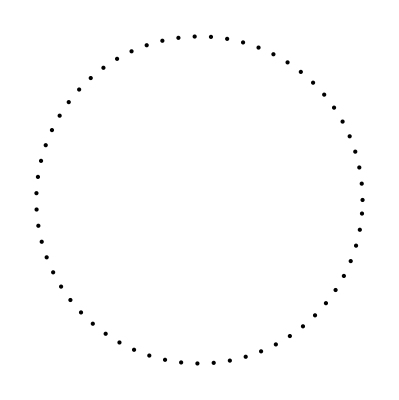
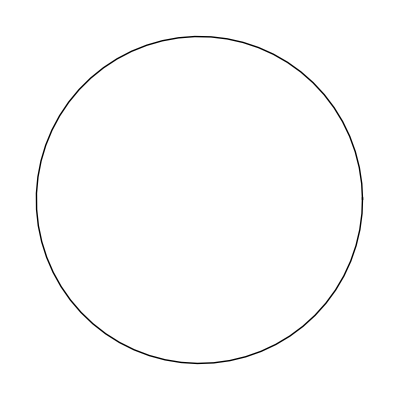

```mathematica
radius = 100;
{Graphics[Table[Point[{radius * Cos[angle], radius * Sin[angle]}],{angle,0,2 Pi,0.1}]],Graphics[Line[{Table[{radius * Cos[a],radius * Sin[a]},{a,0,2 Pi+0.1,0.1}]}]]}
```

Now, lets use the formula, | x/a | ^n _ | y/b | ^n = 1 to get x and y coordinates for the Superellipse.

x = |Cos(θ)|^2/n * angle * sgn(Cos(θ))
y= |Sin(θ)|^2/n * angle * sgn(Sin(θ))
(https://en.wikipedia.org/wiki/Superellipse)

However, before we started that, we need a new function called sgn which basically return 1,-1 or 0 based on value it receives.

Create the sgn function:

```mathematica
sgn[val_] := If[val>0,1,-1,0];
```

Now, lets create our Superellipse with new variables aAngle and bAngle which manipulates shape of the Superellipse:

```mathematica
getLinesForSuperellipse[n_:4] := 
	Module[{aAngle = 100,bAngle = 100},
		Line[{Table[{
			Power[Abs[Cos[angle]],2/n] * aAngle * sgn[Cos[angle]],
			Power[Abs[Sin[angle]],2/n] * bAngle * sgn[Sin[angle]]},
			{angle,0,2 Pi+0.1,0.1}
	]}]]
```

Create a Superellipse using above formula:

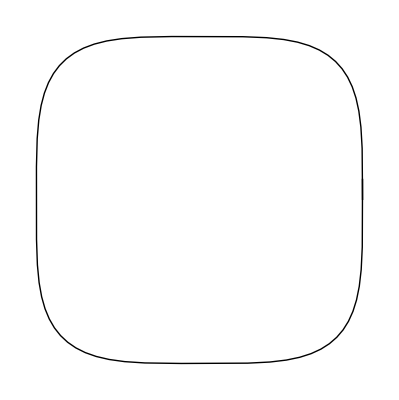

```mathematica
Graphics[getLinesForSuperellipse[]]
```

Let’s look at animation of Superellipse by changing some variables:

```mathematica
Animate[Graphics[getLinesForSuperellipse[n]],{n,0.5,4,.1},AnimationRunning->False,DefaultDuration->2]
```

In this section, we created a circle and then we used a new formula to create a Superellipse.

## Super Shapes in 2D

In the last section, we looked at the circle and the superellipse. Here, we will take a similar look on a 2D circle using a different formula that was introduced by Paul Bourke to create Super shapes in 2D

Below we have the formula to simulate Super shape

-Graphics-
By using this formula, we will change the radius to simulate super shapes.

Let’s create our function to use the formula above:

```mathematica
a = 1; (*a angle*)
b = 1; (*b angle*)
superShape2D[theta_,m_,n1_,n2_,n3_] := 
	Module[{thet = theta},
		part1 = Power[Abs[(1 / a) * Cos[thet * m / 4]],n2];
		part2 = Power[Abs[(1 / b) * Sin[thet * m / 4]],n3];
		part3 = Power[part1 + part2, 1 / n1];
		If[part3 == 0, 0, 1/part3]
	]
```

By using the superShape2D function, we can find x and y coordinates and then use those points to draw lines:

```mathematica
getLinesForSuperShape[m_,n1_,n2_,n3_] := 
	Line[
		{Table[
		{radius * superShape2D[angle,m,n1,n2,n3] *Cos[angle],
		radius * superShape2D[angle,m,n1,n2,n3] *Sin[angle]},
		{angle,-2 Pi,2 Pi,0.005}
	]}];
```

Once we are done with implementing our functions, we can use it to create our Super Shapes:

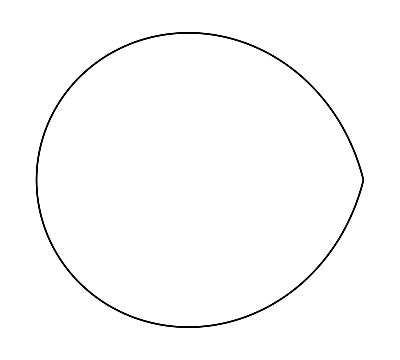
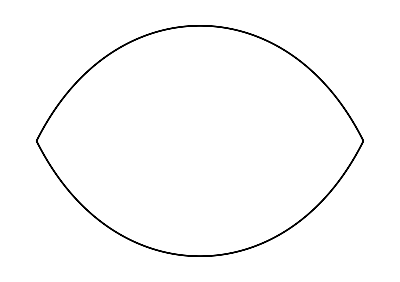
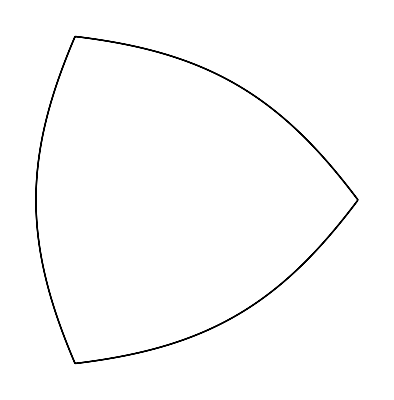
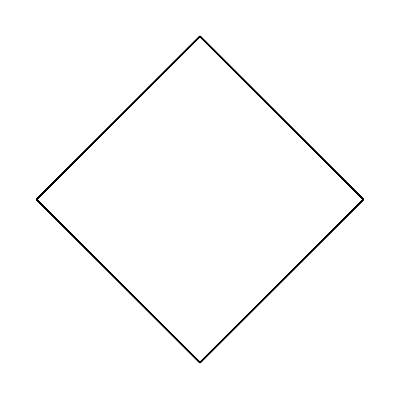

```mathematica
Table[Graphics[getLinesForSuperShape[m,1,1,1]],{m,1,4}]
```

We can change variables to draw different super shapes: (Check conclusion for more examples of super shapes.)

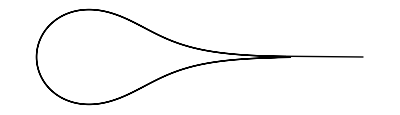
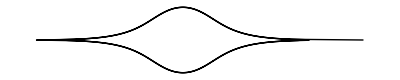
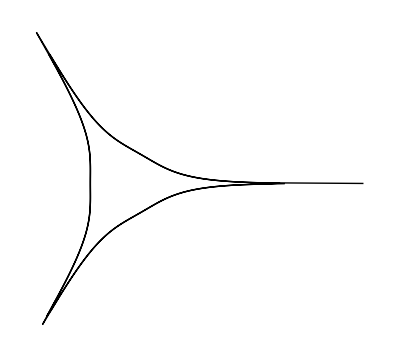
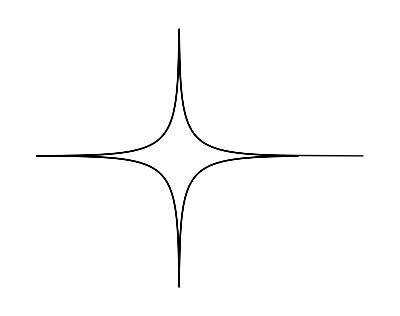

```mathematica
Table[Graphics[getLinesForSuperShape[m,0.3,0.3,0.3]],{m,1,4}]
```

## Super Shapes in 3D

Now, we will try all of what we have done in last 2 sections to create a 3D super shape.

Let’s first plot points on a Sphere using the equation:
-Graphics-

Create a Sphere with points using the above formula:

```mathematica
Graphics3D[
 Table[Point[{radius * Sin[lat]*Cos[lon], radius * Sin[lat]*Sin[lon], radius*Cos[lat]}],
          {lat, 0, Pi , 0.2}, {lon, 0, 2 Pi , 0.1}]]
```

-Graphics3D-

So far we were able to plot points on a sphere. Now we will use the equations below to find  x, y and z coordinates as well as radius to simulate Super Shapes in 3D.

-Graphics-

-Graphics-

Before we move on, let’s clear our history so we will not have any issues or bugs while implementing further functions.

Create a map function to find latitude and longitude.

```mathematica
ClearAll["Global`*"]
map[n_, start1_,stop1_,start2_,stop2_] := ((n-start1)/(stop1-start1))*(stop2-start2)+start2;
```

Create superShape3D function to find out our r1 and r2:

```mathematica
a = 1;
b = 1;
superShape3D[thate_,list_List] := 
Module[{t1,t2,t3,m=First[list],n1=Part[list,2],n2=Part[list,3],n3=Part[list,4]},
	t1 = Power[Abs[(1/a)*Cos[m * thate / 4]],n2];
	t2 = Power[Abs[(1/b)*Sin[m * thate / 4]],n3];
	t3 = t1 +  t2;
	Power[t3,-1/n1]
];
```

Now, it is time to collect all of what we have done in this section into a function to get points for x, y and z coordinates:

```mathematica
createPoints[total_, r_,superShape1_List,superShape2_List] := 
Table[
	With[{
	lat = map[i,0, total,-Pi/2, Pi/2],
	lon = map[j,0, total, -Pi, Pi]
	},With[{
	r1 = superShape3D[lon,superShape1],
	r2 = superShape3D[lat,superShape2]},
	{r*r1*Cos[lon]*r2*Cos[lat],r*r1*Sin[lon]*r2*Cos[lat],r*r2*Sin[lat]}]
	], 
	{i, 1, total+1}, 
	{j, 1, total+1}
]
```

Once we have the points, we can use them to create triangles on a sphere:

```mathematica
createTriangles[{p1_,p2_},{p3_,p4_}] := {Triangle[{p1,p3,p4}],Triangle[{p1,p2,p4}]};
applyGraphics[total_:100,r_:200,superShape1_List,superShape2_List] := 
	Graphics3D[
	Flatten[Apply[createTriangles,Partition[N@createPoints[total,r,superShape1,superShape2],{2,2},1],{2}]]
	,Boxed->False]
```

Examples:

```mathematica
applyGraphics[100,200,{7,0.2,1.7,1.7},{7,0.2,1.7,1.7}]
```

-Graphics3D-

SuperShape 1 : m = 7, n1 = 0.2, n2 = 1.7, n3 = 1.7
SuperShape 2 : m = 7, n1 = 0.2, n2 = 1.7, n3 = 1.7

```mathematica
applyGraphics[50,200,{8,60,100,20},{2,10,10,10}]
```

-Graphics3D-

SuperShape 1 : m = 8, n1 = 60, n2 = 100, n3 = 20
SuperShape 2 : m = 2, n1 = 10, n2 = 10, n3 = 10

```mathematica
applyGraphics[60,200,{2,0.7,0.3,0.2},{3,100,100,100}]
```

-Graphics3D-

SuperShape 1 : m = 2, n1 = 0.7, n2 = 0.3, n3 = 0.2
SuperShape 2 : m = 3, n1 = 100, n2 = 100, n3 = 100

## Conclusion

In this paper, we used some math formulas to create Superellipse and Super shapes.

More of the Super shape formulas and examples could be found in the links below:

http : // paulbourke.net/geometry/supershape/

https://www.youtube.com/watch?v=akM4wMZIBWg&index=4&list=PLRqwX-V7Uu6a5MvGn7a1y4dAKWzM8_Ar0

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com